```mathematica
ClearAll["Global`*"];

v[s_] = c*Sin[n*Pi*s/l];
αcr = α/.Solve[v''''[s]+α^2*v''[s]+β*Pi^4/l^4*v[s]==0, α][[2]]//Simplify
```

(π √(n^4+β))/(l n)

```mathematica
αcr^2
```

(π^2 (n^4+β))/(l^2 n^2)

```mathematica
λcr = αcr^2/Pi^2*l^2
```

(n^4+β)/n^2

```mathematica
n/.Solve[D[λcr, n]==0, n]//Last
```

β^(1/4)

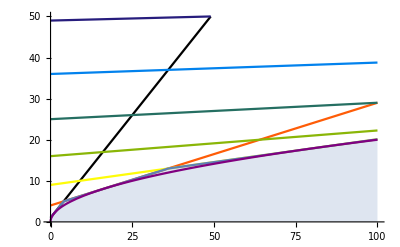

```mathematica
Show[
Plot[Evaluate[Table[λcr, {n,1, 10}]], {β, 0, 100}, PlotStyle->ColorData[3, "ColorList"],PlotRange->{Automatic, {0,50}}],
Plot[Min[Evaluate[Table[n^2+β/n^2, {n,1, 10}]]], {β, 0, 100}, PlotStyle->Automatic, Filling->Axis],
Plot[Sqrt[β]+β/Sqrt[β], {β, 0, 100}, PlotStyle->Purple]
]
```